```mathematica
MyPower[p_,n_]:=MyPower[p,n] = p^n
```

```mathematica
Distance[n_,p_] := Module[ {threshold, digits, position, found, nextPower, result},
If [n ==0, Return[0]];
(* Initialize some precomputed local varables *)
threshold = (p-1)/2;
digits = IntegerDigits[n,p];

(* find the first digit above the threshold *)
found = -1;
For[ position = 1, position <=Length[digits], position++,
If [ digits [[position]] > threshold,
found = position; Break[]
]
];

(* if we didn't find a digit, then the distance is zero *)
If [found ==-1, Return[0]];

(* we did find a faulty digit.  Now we need to look before it for digits that equal the threshold.
If we would not coun these then we would end up with a new value which is still not p-good (due
to the carrying) *)
While[ found >1,
If [ digits [[found-1]] == threshold,found --,Break[]]
];

(* if we have gone all the way to the start*)
If[found ==1,
Block[{},
nextPower= MyPower[p,(Length[digits])];
Return[nextPower-n]
]
];


nextPower=MyPower[ p,(Length[digits]+1-found)];
Return[nextPower-FromDigits[Take[digits,-(Length[digits]+1-found)],p]]
]
```

```mathematica
FileNameForTuple[ primes_] := Module[{fileName, temp, sep, p, pPos},
sep = "\\";
temp ="d:\\triangle\DataSrc";
For[pPos =1, pPos <= Length[primes], pPos++,
temp = StringJoin[temp, sep, ToString[primes[[pPos]]]];
];
temp = StringJoin[temp, "\\Solutions.txt"];
fileName = temp;
Return[fileName]
]
```

```mathematica
countFound=0
```

0

```mathematica
lastValue=-1
```

-1

```mathematica
KnownMaximum[primes_] := KnownMaximum[primes] =Module[{result, fileName, list},
If[lastValue==-1,
fileName = FileNameForTuple[primes];
If [FileExistsQ[fileName],
PrintTemporary["Reading :" <> fileName <> " ..."];
list = ReadList[fileName, Number];
PrintTemporary["Done." ];
countFound = Length[list];
lastValue =Max[list];
,
lastValue =-1
]
];
Return[lastValue];
]
```

```mathematica
AlgoList[start_, end_, primes_] := Module[{result, current,  maxdist, last},
last = KnownMaximum[primes];
current=start;
If[last >= end,
(*PrintTemporary[ToString[ScientificForm[end+0.1,10]] <> " is smaller than " <> ToString[ScientificForm[last+0.001,10]]];*)
Return[{}],
If [last > start,
current = last +1;
PrintTemporary["Starting at " <> ToString[ScientificForm[current,10]]];
,
current = start
]
];
result = {};
While[current ≤ end,
(*Print[current];*)
maxdist = Max[ParallelTable[Distance[current, p], {p, primes}]];
If[maxdist==0,
With[{f=OpenAppend[FileNameForTuple[primes], PageWidth->2000]},
Write[f,current];
Close[f];
];
result = {current};
lastValue = current;
current +=1;
If[Mod[countFound,1000]==0, PrintTemporary[ToString[countFound] <> " - " <> ToString[lastValue]]];
countFound++;
,
current += maxdist;
];
];
Return [result];
]
```

```mathematica
Examine[list_] := Module[{result, current, previous, pos},
result = 0;
previous = -100;
For[pos=1, pos ≤ Length[list], pos++,
If[Mod[pos,100000]==0, PrintTemporary[ToString[pos] <> " - " <> ToString[Length[list]]]];
current = list[[pos]];
If [current == previous+1,
result +=1
];
previous = current;
];
Return  [result];
]
```

```mathematica
(*Timing[For[i=2193,i≤50000,i+=4,Print[{i,Timing[ParallelTable[AlgoList[10^j-1,10^(j+1),{7,11,13,19}],{j,i,i+3}]]}]]]*)
```

```mathematica
Timing[For[i=0,i≤50000,i+=4,PrintTemporary[{i,Timing[Table[AlgoList[10^j-1,10^(j+1),{3,5,7}],{j,i,i+3}]]}]]]
```

$Aborted

```mathematica
With[
{
g=GoodForTuple[{3,5,7}]
},
N[Examine[g]/Length[g]]
]
```

0.249939

```mathematica
With[
{g=ReadList[FileNameForTuple[{7,11,13,19}]]},
N[Examine[g]/Length[g]]
]
```

0.477074

```mathematica
FileNameForTuple[{7,11,13,19}]
```

d:\triangle\DataSrc\7\11\13\19\Solutions.txt

```mathematica
With[
{g=GoodForTuple[{3,5,7}]},
Sort[Tally[ParallelTable[Last[IntegerDigits[v]], {v,g}]]]
]
```

{{0,1200549},{1,1200379},{2,1201963},{5,1199674},{6,1200528},{7,1198422}}

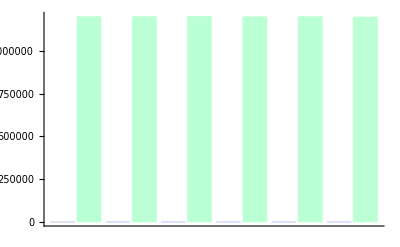

```mathematica
BarChart[{{0,1200549},{1,1200379},{2,1201963},{5,1199674},{6,1200528},{7,1198422}}]
```

```mathematica
Length[Subsets[Prime[Range[2,9]],{2,9}]]
```

```mathematica
247*15000
```

3705000

```mathematica
Prime[Range[15,17]]
```

{47,53,59}